NDSolve::eerr: Warning: scaled local spatial error estimate of 5.23111×10^7 at t = 2.×10^-11 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 301 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in t1 near {t1} = {1.3987×10^-13}. NIntegrate obtained 220.572 and 0.00104897 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in t1 near {t1} = {1.43984×10^-13}. NIntegrate obtained 190.568 and 0.000549014 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in t1 near {t1} = {1.02391×10^-13}. NIntegrate obtained 104.43 and 0.004685 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1.07012×10^7 at t = 2.×10^-11 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 301 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 8 recursive bisections in t1 near {t1} = {1.27214×10^-13}. NIntegrate obtained 65.0552 and 0.000454193 for the integral and error estimates.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1.22647×10^9 at t = 2.×10^-11 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 301 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

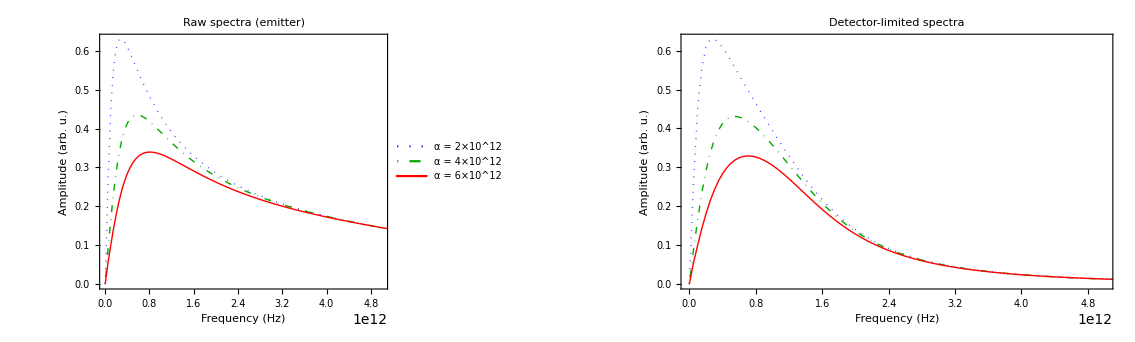

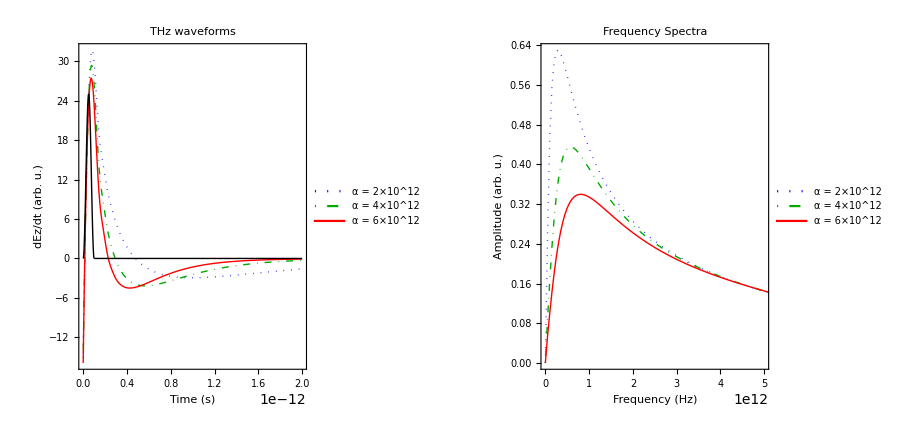

```mathematica
(* ::Title::*)
(*Phonon Drag THz Emission-Gold Parameters*)
(* ::Subtitle::*)(*Simulation of THz waveforms and spectra from laser-excited metals*)
(* ::Author::*)
(*Ivan Oladyshkin,IAP RAS*)
(* ::Date::*)(*04.2026*)

(*Initialization*)
ClearAll["Global`*"];

(*Physical constants*)
cl=3*10^10;        (*speed of light,cm/s*)
c=3.2*10^5;        (*speed of sound,cm/s*)
G=1*10^12;       (*electron-phonon thermalization rate,1/s*)
c0=1.29*10^6;      (*lattice heat capacity,erg/(cm^3 K)*)
ro=19.3;           (*density,g/cm^3*)
el=4.8*10^(-10);   (*electron charge,statC*)
T0=300;            (*initial temperature,K*)
EF=5.5*1.6*10^(-12); (*Fermi energy,erg*)
kB=1.38*10^(-16);  (*Boltzmann constant,erg/K*)
Nue=50*10^13;      (*electron collision frequency,1/s*)
me=9.1*10^(-28);   (*electron mass,g*)
omega=2.3*10^15;   (*laser frequency,1/s*)
VF=Sqrt[2*EF/me];  (*Fermi velocity,cm/s*)
ne=0.59*10^23;     (*electron density,1/cm^3*)
kappa=17.4*10^5;   (*thermal conductivity,erg/(cm s K)*)

(*Derived quantities*)
DT=VF^2/(3*Nue);   (*electron diffusivity,cm^2/s*)
DL=kappa/(c0*ro);  (*lattice diffusivity,cm^2/s*)

(*Laser and geometry parameters*)
alfaEl=1*10^12;    (*ph-e collision rate,1/s*)
tau=1*10^(-13);    (*full pulse duration,s*)
lsk=1.2*10^(-6);   (*skin depth,cm*)
x0=-5*10^(-5);     (*left boundary,cm*)
t0=20*10^(-12);    (*simulation time,s*)
R=0.3;             (*reflectivity*)
Rlight=0.9;        (*light reflectivity*)
delay=0;           (*pulse delay,s*)

(*Optical source term*)
Source[x_,t_]:=Piecewise[{{((1-Rlight)*100*10^4*Sin[Pi*(t-delay)/tau]^2)*Exp[x/lsk],t>=delay&&t<=delay+tau}},0];

(* ::Section::*)
(*Solver*)

(*Phonon damping rates*)
alfaValues={1*10^12,3*10^12,5*10^12};

solveForAlfa[alfa_]:=Module[{s,PxSol,TeSol,TlSol,EzValues,EzInterp,dEzInterp,tValues,nPoints},s=NDSolve[{D[Tl[x,t],t]==G*((ne*Pi^2*kB^2*Te[x,t]/(2 EF))/(c0*ro))*(Te[x,t]-Tl[x,t])-(c^2/(c0*ro))*D[Px[x,t],x],D[Te[x,t],t]==(8*EF*el^2*Nue/(Pi*Te[x,t]*kB^2*tau*cl*me*omega^2))*Source[x,t]-G*(Te[x,t]-Tl[x,t])+DT*D[Te[x,t],x,x],
D[Px[x,t],t]==-(c0*ro/3)*D[Tl[x,t],x]-alfa*Px[x,t],

(*Initial conditions*)
Te[x,0]==T0,Tl[x,0]==T0,Px[x,0]==0,
(*Boundary conditions*)
Derivative[1,0][Te][x0,t]==0,Derivative[1,0][Te][0,t]==0,Px[x0,t]==0,Px[0,t]==0},{Te,Tl,Px},{x,x0,0},{t,0,t0},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->300,"MaxPoints"->600,"DifferenceOrder"->2},"DifferentiateBoundaryConditions"->{True,"ScaleFactor"->100}},MaxSteps->500000,AccuracyGoal->8,PrecisionGoal->8];
{PxSol,TeSol,TlSol}={Px,Te,Tl}/. s[[1]];
(*THz field reconstruction*)nPoints=500;
tValues=Table[t,{t,0,t0,t0/(nPoints-1)}];
EzValues=Table[300*(0.1/cl)*(alfaEl*c0*ro/(3*ne*el))*Exp[-alfa*t]*NIntegrate[D[TlSol[0,t1],t1]*Exp[alfa*t1],{t1,0,t},Method->{"GlobalAdaptive",Method->"GaussKronrodRule","SymbolicProcessing"->0,"MaxErrorIncreases"->500},AccuracyGoal->6,PrecisionGoal->6,MaxRecursion->8],{t,tValues}];
EzInterp=Interpolation[Transpose[{tValues,EzValues}],Method->"Spline",InterpolationOrder->5];
dEzInterp[t_]:=D[EzInterp[tt],tt]/. tt->t;
{dEzInterp,tValues}];

(* ::Section::*)
(*Data generation*)

{interp1,tVals1}=solveForAlfa[alfaValues[[1]]];
{interp2,tVals2}=solveForAlfa[alfaValues[[2]]];
{interp3,tVals3}=solveForAlfa[alfaValues[[3]]];

scale=10^10;  (*arbitrary units scaling*)

(* ::Section::*)
(*Visualization*)

(*Time domain waveforms*)
plot1=Plot[{interp1[t]/scale,interp2[t]/scale,interp3[t]/scale,(25*Source[0,t]/10^5)},{t,0,2*10^-12},PlotRange->All,PlotStyle->{{Blue,Thick,Dotted},{Darker[Green],Thick,DotDashed},{Red,Thick},{Black,Thick}},Frame->True,FrameLabel->{"Time (s)","dE\!\(\*SubscriptBox[\(z\), \(\)]\)/dt (arb. u.)"},PlotLabel->"THz waveforms",PlotLegends->Placed[LineLegend[{"α = 2×10^12","α = 4×10^12","α = 6×10^12"},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->LightGray]&)],{0.8,0.8}],ImageSize->400,LabelStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Thick];

(*Spectrum calculation*)
computeSpectrum[dEzInterp_,tMin_,tMax_,nPoints_]:=Module[{tData,ezData,ezData2,dt,samplingRate,ft,freqs,amplitudeSpectrum},tData=Subdivide[tMin,tMax,nPoints-1];
ezData=Table[dEzInterp[t],{t,tData}];
ezData2=ezData-Mean[ezData];(*remove DC component*)dt=(tMax-tMin)/(nPoints-1);
samplingRate=1/dt;
ft=Fourier[ezData2,FourierParameters->{1,-1}];
freqs=Range[0,nPoints/2-1]*(samplingRate/nPoints);
amplitudeSpectrum=(2/nPoints)*Abs[ft[[1;;nPoints/2]]];
Transpose[{freqs,amplitudeSpectrum}]];

tMin=0;
tMax=t0;
nPoints=2^10;

spec1=computeSpectrum[interp1,tMin,tMax,nPoints];
spec2=computeSpectrum[interp2,tMin,tMax,nPoints];
spec3=computeSpectrum[interp3,tMin,tMax,nPoints];

scaleSpec[spec_]:={#[[1]],#[[2]]/scale}&/@spec;

spec1scaled=scaleSpec[spec1];
spec2scaled=scaleSpec[spec2];
spec3scaled=scaleSpec[spec3];

(*Detector response function (ZnTe,1 mm)*)(*Parameters:only high-frequency roll-off,low frequencies unchanged*)

nuCut=1.5*10^12;   (*cutoff frequency,Hz*)
Rdet[nu_]:=1/Sqrt[1+(nu/nuCut)^4];

(*Apply detector response to spectra*)
spec1det={#[[1]],#[[2]]*Rdet[#[[1]]]}&/@spec1scaled;
spec2det={#[[1]],#[[2]]*Rdet[#[[1]]]}&/@spec2scaled;
spec3det={#[[1]],#[[2]]*Rdet[#[[1]]]}&/@spec3scaled;

(* ::Section::*)
(*Visualization of detector response*)

(*Plot detector response function*)
plotRdet=Plot[Rdet[nu],{nu,0,5*10^12},PlotStyle->{Black,Thick,Dashed},Frame->True,FrameLabel->{"Frequency (Hz)","R\_det (arb. u.)"},PlotLabel->"Detector response",ImageSize->400,LabelStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Thick];

(* ::Section::*)
(*Comparison:raw vs detector-limited spectra*)

(*Raw spectra (as before)*)
plotRaw=ListLinePlot[{spec1scaled,spec2scaled,spec3scaled},PlotRange->{{0,5*10^12},All},PlotStyle->{{Blue,Thick,Dotted},{Darker[Green],Thick,DotDashed},{Red,Thick}},Frame->True,FrameLabel->{"Frequency (Hz)","Amplitude (arb. u.)"},PlotLabel->"Raw spectra (emitter)",PlotLegends->Placed[LineLegend[{"α = 2×10^12","α = 4×10^12","α = 6×10^12"},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->LightGray]&)],{0.8,0.8}],ImageSize->400,LabelStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Thick];

(*Detector-limited spectra*)
plotDet=ListLinePlot[{spec1det,spec2det,spec3det},PlotRange->{{0,5*10^12},All},PlotStyle->{{Blue,Thick,Dotted},{Darker[Green],Thick,DotDashed},{Red,Thick}},Frame->True,FrameLabel->{"Frequency (Hz)","Amplitude (arb. u.)"},PlotLabel->"Detector-limited spectra",ImageSize->400,LabelStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Thick];

(* ::Section::*)
(*Combined figure:raw+detector-limited*)

GraphicsRow[{plotRaw,plotDet},Spacings->20,ImageSize->900]

(*Optional:overlay of raw and detector-limited for one alpha*)
plotOverlay=ListLinePlot[{spec1scaled,spec1det},PlotRange->{{0,5*10^12},All},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed}},Frame->True,FrameLabel->{"Frequency (Hz)","Amplitude (arb. u.)"},PlotLabel->"Raw vs detector-limited (α = 2×10^12)",PlotLegends->Placed[LineLegend[{"Raw (emitter)","Detector-limited"},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->LightGray]&)],{0.8,0.8}],ImageSize->400,LabelStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Thick];

(*Frequency spectra*)
plot2scaled=ListLinePlot[{spec1scaled,spec2scaled,spec3scaled},PlotRange->{{0,5*10^12},All},PlotStyle->{{Blue,Thick,Dotted},{Darker[Green],Thick,DotDashed},{Red,Thick}},Frame->True,FrameLabel->{"Frequency (Hz)","Amplitude (arb. u.)"},PlotLabel->"Frequency Spectra",PlotLegends->Placed[LineLegend[{"α = 2×10^12","α = 4×10^12","α = 6×10^12"},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->LightGray]&)],{0.8,0.8}],ImageSize->400,LabelStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Thick];

(*Final figure*)
GraphicsRow[{plot1,plot2scaled},Spacings->20,ImageSize->900]

(* ::Section::*)
(*Export (optional)*)
(*Export["THz_spectra.pdf",GraphicsRow[{plot1,plot2scaled},Spacings->20,ImageSize->900]];*)
```